FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

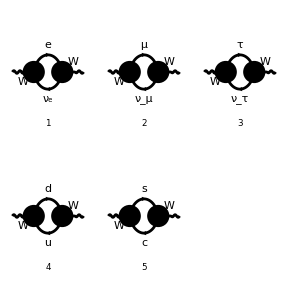

FeynArtsGraphics()(([1] | [2] | [3]
[4] | [5] | Null
Null | Null | Null))

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts= True;
<< FeynCalc`

$FAVerbose=0;
SetOptions[Paint,SheetHeader -> None, Numbering -> Simple];

$BreitMaison=False;
$Larin=False;
$West=True;

(*creating fermionic loops*)
topoself=CreateTopologies[1,1-> 1,SelfEnergiesOnly];
process0=V[3]-> V[3];
fpudcs=InsertFields[topoself,process0,InsertionLevel->{Particles},ExcludeParticles->{V[1],V[2],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[3,{3}],F[4,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[fpudcs,SheetHeader->False]
(*creating amplitudes*)
fself1=CreateFeynAmp[fpudcs, Truncated-> True, PreFactor ->-1,GaugeRules-> {}];

ampfself1=FCFAConvert[fself1, List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> True, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0,SMP["m_tau"]->0,SMP["e"]-> Sqrt[4Pi SMP["alpha_fs"]]}]//Contract//FCTraceFactor;

transverse1=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampfself1//Contract//DiracSimplify;
```

```mathematica
ΣWWlightfermion[k_]=-ⅈ/(16 π^2)TID[transverse1/.DiracTrace->Tr,q,ToPaVe-> True]/.SumOver[SUNFIndex[Col3],3]-> 3/.Pair[Momentum[k,D],Momentum[k,D]]-> k^2//DiracSimplify
```

(9 π α (2-D) k^2 B_0(k^2,0,0))/(8 (1-D) (sin(θ_W))^2)

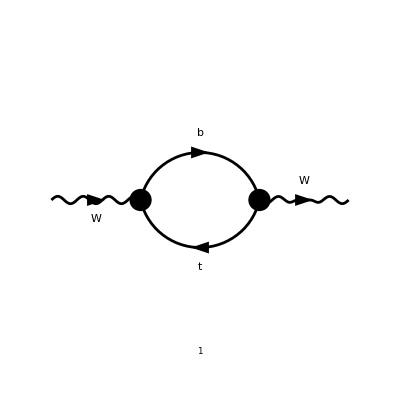

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
fptb=InsertFields[topoself,process0,InsertionLevel->{Particles},ExcludeParticles->{F[1],F[2],F[2,{3}],V[1],V[2],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[3,{1}],F[3,{2}],F[4,{2}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[fptb,SheetHeader->False]
```

```mathematica
fself3=CreateFeynAmp[fptb, Truncated-> True, PreFactor ->-1,GaugeRules-> {}];
ampfself3=FCFAConvert[fself3, List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> True, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0,SMP["e"]-> Sqrt[4Pi SMP["alpha_fs"]],SumOver[SUNFIndex[Col3],3]-> 3}]//Contract//FCTraceFactor
```

(6 π α tr((m_t-γ·q).γ^ν.(γ̄)^7.(γ·(k-q)).γ^μ.(γ̄)^7))/((sin(θ_W))^2 (q^2-m_t^2).(q-k)^2)

```mathematica
(*using projecting operator to obtain transverse component*)
```

```mathematica
transverse3=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampfself3//Contract//DiracSimplify;
```

```mathematica
(*decomposing transverse component in terms of Passarino-Veltmann basis*)
```

```mathematica
transversewwtop=
-ⅈ/(16 π^2) TID[transverse3/.DiracTrace-> Tr,q,ToPaVe-> True]//FullSimplify
```

(3 π α ((k^2-m_t^2) ((D-2) k^2+m_t^2) B_0(k^2,0,m_t^2)+A_0(m_t^2) (m_t^2-(D-2) k^2)))/(8 (D-1) k^2 (sin(θ_W))^2)

```mathematica
ΣWWtop[k_]=transversewwtop/.Pair[Momentum[k,D],Momentum[k,D]]-> k^2
```

(3 π α ((k^2-m_t^2) ((D-2) k^2+m_t^2) B_0(k^2,0,m_t^2)+A_0(m_t^2) (m_t^2-(D-2) k^2)))/(8 (D-1) k^2 (sin(θ_W))^2)

```mathematica
ΣWW[k_]=ΣWWlightfermion[k]+ΣWWtop[k]/.FCI[rule3]//Expand
```

-(3 π α m_t^4 B_0(k^2,0,m_t^2))/(8 (D-1) k^2 (sin(θ_W))^2)-(3 π α D m_t^2 B_0(k^2,0,m_t^2))/(8 (D-1) (sin(θ_W))^2)+(9 π α m_t^2 B_0(k^2,0,m_t^2))/(8 (D-1) (sin(θ_W))^2)+(3 π α D k^2 B_0(k^2,0,m_t^2))/(8 (D-1) (sin(θ_W))^2)-(3 π α k^2 B_0(k^2,0,m_t^2))/(4 (D-1) (sin(θ_W))^2)-(9 π α D k^2 B_0(k^2,0,0))/(8 (1-D) (sin(θ_W))^2)+(9 π α k^2 B_0(k^2,0,0))/(4 (1-D) (sin(θ_W))^2)+(3 π α m_t^2 A_0(m_t^2))/(8 (D-1) k^2 (sin(θ_W))^2)-(3 π α D A_0(m_t^2))/(8 (D-1) (sin(θ_W))^2)+(3 π α A_0(m_t^2))/(4 (D-1) (sin(θ_W))^2)

```mathematica
(*define a differential transverse function of WW propagator in terms k*)
```

```mathematica
dΣWW[k_]=D[ΣWW[k],Pair[Momentum[k,D],Momentum[k,D]]]/. Pair[Momentum[k,D],Momentum[k,D]]-> k^2
```

0

```mathematica
(*using series expansion for obtaining ΣWW(0)*)
```

```mathematica
ΣWW[0]=Normal[Series[ΣWW[k],{k,0,0}]]/.FCI[rule3]/.k-> 0//Expand
```

(15 π α A_0(m_t^2))/(8 (D-1) (sin(θ_W))^2)-(3 π α D A_0(m_t^2))/(4 (D-1) (sin(θ_W))^2)

```mathematica
ΣWW[0]=Normal[Series[ΣWW[k]/.k^2->s ,{s,0,1}]]/.FCI[rule3]/.s-> 0//Expand
```

(15 π α A_0(m_t^2))/(8 (D-1) (sin(θ_W))^2)-(3 π α D A_0(m_t^2))/(4 (D-1) (sin(θ_W))^2)

```mathematica
Collect[ΣWW[SMP["m_W"]]/.FCI[rule3],{B0[SMP["m_W"]^2,0,0],A0[SMP["m_t"]^2],B0[SMP["m_Z"]^2,0,0],B0[SMP["m_W"]^2,0,SMP["m_t"]^2]}]/. 1/SMP["sin_W"]^2-> 1/(1-SMP["m_W"]^2/SMP["m_Z"]^2)
```

B_0(m_W^2,0,m_t^2) (-(3 π α m_t^4)/(8 (D-1) m_W^2 (1-m_W^2/m_Z^2))-(3 π α D m_t^2)/(8 (D-1) (1-m_W^2/m_Z^2))+(9 π α m_t^2)/(8 (D-1) (1-m_W^2/m_Z^2))+(3 π α D m_W^2)/(8 (D-1) (1-m_W^2/m_Z^2))-(3 π α m_W^2)/(4 (D-1) (1-m_W^2/m_Z^2)))+B_0(m_W^2,0,0) ((9 π α m_W^2)/(4 (1-D) (1-m_W^2/m_Z^2))-(9 π α D m_W^2)/(8 (1-D) (1-m_W^2/m_Z^2)))+A_0(m_t^2) ((3 π α m_t^2)/(8 (D-1) m_W^2 (1-m_W^2/m_Z^2))-(3 π α D)/(8 (D-1) (1-m_W^2/m_Z^2))+(3 π α)/(4 (D-1) (1-m_W^2/m_Z^2)))

```mathematica
uvsigww0=PaXEvaluateUV[ΣWW[0]]
```

-(3 π α m_t^2)/(8 ε_UV (sin(θ_W))^2)

```mathematica
uvsigwwmw=PaXEvaluateUV[ΣWW[SMP["m_W"]]]
```

-(π α (3 m_t^2-8 m_W^2))/(8 ε_UV (sin(θ_W))^2)

```mathematica
(*special treatment for ΣWW[k^2=0]. Instead of using projection operator, we us 1/D Subscript[g, μν] to avoid the embarassing 1/k^2.*)
```

```mathematica
Σd=1/D(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]. ampfself1+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]. ampfself3)/. SumOver[SUNFIndex[Col3],3]-> 3//Contract//DiracSimplify
```

(6 π α tr(-D q^2 (γ̄)^7+2 q^2 (γ̄)^7+1/2 D (k·q)-k·q))/(D (sin(θ_W))^2 (q^2-m_t^2).(q-k)^2)-(18 π α tr(D q^2 (γ̄)^7-2 q^2 (γ̄)^7-1/2 D (k·q)+k·q))/(D q^2.(q-k)^2 (sin(θ_W))^2)

```mathematica
Σd1=-ⅈ/(16 π^2)TID[Σd/.DiracTrace-> Tr,q,ToPaVe-> True]//FullSimplify
```

-(3 π α (D-2) ((m_t^2-k^2) B_0(k^2,0,m_t^2)-3 k^2 B_0(k^2,0,0)+A_0(m_t^2)))/(8 D (sin(θ_W))^2)

```mathematica
Σd0=Σd1/.Pair[Momentum[k,D],Momentum[k,D]]-> 0/.FCI[rule3]
```

-(3 π α (D-2) A_0(m_t^2))/(4 D (sin(θ_W))^2)